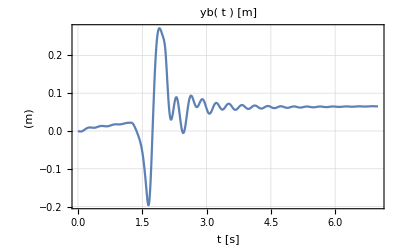

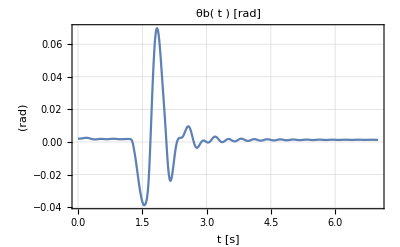

```mathematica
f=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\dataVz.txt"];
data1=ReadList[f,{Number,Number}];
Close[f];
a=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\data_Pitch_Angle.txt"];
data3=ReadList[a,{Number,Number}];
Close[a];

(* Deslocamento de dados da velocidade para que a integral (deslocamento) seja mais coerente *)
data2 =Subtract[data1,{{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083}}];

data4 = Times[data3, {{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)}}];

velocidade1= Interpolation[data1];
vz= Interpolation[data2];
z1[t] = Integrate[velocidade1[t],t];
dz[t] =Integrate[vz[t],t];

angle = Interpolation[data4];

omega[t] = D[angle[t],t];
Plot[dz[t],{t, 0,7}, PlotRange->All, PlotLabel->"yb( t )  [m]", LabelStyle->"Subsubsection", Frame->True, GridLines->Automatic, AxesLabel->{"t [s]","(m)"}]

Plot[angle[t],{t, 0,7}, PlotRange->All, PlotLabel->"θb( t ) [rad]", LabelStyle->"Subsubsection", Frame->True, GridLines->Automatic, AxesLabel->{"t [s]","(rad)"}]
```

```mathematica
xC1 = lot/2*Cos[θot[t]];
xB1 = lb/2*Cos[θb[t]] + li*(Cos[θb[t]]*Cos[θ1[t]]-Sin[θb[t]]*Sin[θ1[t]]);
zC1 = zot[t] + lot/2*Sin[θot[t]];
zB1 = zb[t] + lb/2*Sin[θb[t]] + li*(Sin[θb[t]]*Cos[θ1[t]]+Sin[θ1[t]]*Cos[θb[t]]);
xC2 = -lot/2*Cos[θot[t]];
xB2 = -lb/2*Cos[θb[t]] + li*(Cos[θb[t]]*Cos[θ2[t]]-Sin[θb[t]]*Sin[θ2[t]]);
zC2 = zot[t] - lot/2*Sin[θot[t]];
zB2 = zb[t] - lb/2*Sin[θb[t]] + li*(Sin[θb[t]]*Cos[θ2[t]]+Cos[θb[t]]*Sin[θ2[t]]);

h1 = (xB1 - xC1)^2+ (zC1 - zB1)^2 - ls^2 ;
h2 = (xC2 - xB2)^2+ (zC2 - zB2)^2 - ls^2 ;

h1expaux=Expand[h1];
h2expaux=Expand[h2];

h1dot = Expand[D[h1,t]];
h2dot = Expand[D[h2,t]];

h1dot2=Expand[D[h1,{t,2}]];
h2dot2 = Expand[D[h2,{t,2}]];

A = ({{D[h1dot,zot'[t]], D[h1dot,θot'[t]], D[h1dot,θ1'[t]], D[h1dot,θ2'[t]]}, {D[h2dot,zot'[t]], D[h2dot,θot'[t]], D[h2dot,θ1'[t]], D[h2dot,θ2'[t]]}});
MatrixForm[A]
At = Transpose[A];
MatrixForm[At];
λ=({{λ1[t]}, {λ2[t]}});
qdot = {{zot'[t],θot'[t],θ1'[t],θ2'[t]}};
qdot.At.λ;
```

(-2 li Cos[θb[t]] Sin[θ1[t]]-lb Sin[θb[t]]-2 li Cos[θ1[t]] Sin[θb[t]]+lot Sin[θot[t]]-2 zb[t]+2 zot[t] | -li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]-li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]+li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]-lot Cos[θot[t]] zb[t]+lot Cos[θot[t]] zot[t] | -lb li Cos[θb[t]]^2 Sin[θ1[t]]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]-lb li Sin[θ1[t]] Sin[θb[t]]^2-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θ1[t]] Cos[θb[t]] zb[t]-2 li Sin[θ1[t]] Sin[θb[t]] zb[t]-2 li Cos[θ1[t]] Cos[θb[t]] zot[t]+2 li Sin[θ1[t]] Sin[θb[t]] zot[t] | 0
-2 li Cos[θb[t]] Sin[θ2[t]]+lb Sin[θb[t]]-2 li Cos[θ2[t]] Sin[θb[t]]-lot Sin[θot[t]]-2 zb[t]+2 zot[t] | li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]+li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]-li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]+lot Cos[θot[t]] zb[t]-lot Cos[θot[t]] zot[t] | 0 | lb li Cos[θb[t]]^2 Sin[θ2[t]]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+lb li Sin[θ2[t]] Sin[θb[t]]^2+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θ2[t]] Cos[θb[t]] zb[t]-2 li Sin[θ2[t]] Sin[θb[t]] zb[t]-2 li Cos[θ2[t]] Cos[θb[t]] zot[t]+2 li Sin[θ2[t]] Sin[θb[t]] zot[t])

```mathematica
(* Para o lado direito da maca θ1[t] *)
h1expaux;
h1exp = -ls^2+1/4 lb^2 +lb li Cos[θ1[t]] Cos[θb[t]]^2+li^2 -1/2 lb lot Cos[θb[t]] Cos[θot[t]]-li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]]+1/4 lot^2 +li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]]+lb li Cos[θ1[t]] Sin[θb[t]]^2-li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]]-1/2 lb lot Sin[θb[t]] Sin[θot[t]]-li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θb[t]] Sin[θ1[t]] zb[t]+lb Sin[θb[t]] zb[t]+2 li Cos[θ1[t]] Sin[θb[t]] zb[t]-lot Sin[θot[t]] zb[t]+zb[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] zot[t]-lb Sin[θb[t]] zot[t]-2 li Cos[θ1[t]] Sin[θb[t]] zot[t]+lot Sin[θot[t]] zot[t]-2 zb[t] zot[t]+zot[t]^2;
(* E1 Cos(θ1) + F1 Sin(θ1) + G1 = 0 *)

E1 = D[h1exp,Cos[θ1[t]]];
F1 =D[h1exp,Sin[θ1[t]]];
G1=Expand[h1exp]-Expand[E1*Cos[θ1[t]]]-Expand[F1*Sin[θ1[t]]];
u1 = (-F1+Sqrt[F1^2-G1^2+E1^2])/(G1-E1);
u2 = (-F1-Sqrt[F1^2-G1^2+E1^2])/(G1-E1);
theta11 = ArcCos[(1-u1^2)/(1+u1^2)]; (* configuração B1 posição interna *)
theta12 = ArcCos[(1-u2^2)/(1+u2^2)]; (* configuração B1 posição externa *)

Evaluate[theta11/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, zot[t]->0.2}];
Evaluate[theta12/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, zot[t]->0.38, θb[t]->0, zb[t]->0}]

(* Para o lado esquerdo da maca θ2[t] *)
h2expaux;
h2exp = -ls^2+1/4 lb^2 -lb li Cos[θ2[t]] Cos[θb[t]]^2+li^2 -1/2 lb lot Cos[θb[t]] Cos[θot[t]]+li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]]+1/4 lot^2 -li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]]-lb li Cos[θ2[t]] Sin[θb[t]]^2+li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]]-1/2 lb lot Sin[θb[t]] Sin[θot[t]]+li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θb[t]] Sin[θ2[t]] zb[t]-lb Sin[θb[t]] zb[t]+2 li Cos[θ2[t]] Sin[θb[t]] zb[t]+lot Sin[θot[t]] zb[t]+zb[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] zot[t]+lb Sin[θb[t]] zot[t]-2 li Cos[θ2[t]] Sin[θb[t]] zot[t]-lot Sin[θot[t]] zot[t]-2 zb[t] zot[t]+zot[t]^2;
(* E2 Cos(θ2) + F2 Sin(θ2) + G2 = 0 *)

E2 = D[h2exp,Cos[θ2[t]]];
F2 =D[h2exp,Sin[θ2[t]]];
G2=Expand[h2exp]-Expand[E2*Cos[θ2[t]]]-Expand[F1*Sin[θ2[t]]];
v1 = (-F2+Sqrt[F2^2-G2^2+E2^2])/(G2-E2);
v2 = (-F2-Sqrt[F2^2-G2^2+E2^2])/(G2-E2);
theta21 = ArcCos[(1-v1^2)/(1+v1^2)]; (* configuração B2 posição externa *)
theta22 = ArcCos[(1-v2^2)/(1+v2^2)]; (* configuração B2 posição interna *)
Evaluate[theta21/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, zot[t]->0.38, θb[t]->0, zb[t]->0}]
Evaluate[theta22/.{lb->2,ls->0.3, li->0.2, lot->1.8, θot[t]->0, zot[t]->0.3, θb[t]->0, zb[t]->0}];
```

0.983784

2.15781

```mathematica
(* Termos de Energia *)
T = 1/2 Mot ( D[zot[t],t]^2+ 1/12 lot^2 D[θot[t],t]^2);
V = Mot*g *(zot[t])  + 1/2 k (1.0471975511965903-θ1[t])^2 + 1/2 k (θ2[t]-2.0943951023932046)^2;
R =  1/2 c D[θ1[t],t]^2 + 1/2 c D[θ2[t],t]^2;
P = qdot.At.λ;
H=P[[1]]//First;
```

```mathematica
(* Lagrange com seus multiplicadores *)
𝕢[t_] = {zot[t], θot[t], θ1[t], θ2[t]};
𝕖[t_] = Join[((D[D[T,D[#,t]],t]-D[T,#]+D[V,#]+D[R,D[#,t]]+D[H,D[#,t]]==0) & /@ 𝕢[t]),{(h1dot2==0) , (h2dot2 ==0)}];
𝕖[t]//TableForm
```

g Mot+(-2 li Cos[θb[t]] Sin[θ1[t]]-lb Sin[θb[t]]-2 li Cos[θ1[t]] Sin[θb[t]]+lot Sin[θot[t]]-2 zb[t]+2 zot[t]) λ1[t]+(-2 li Cos[θb[t]] Sin[θ2[t]]+lb Sin[θb[t]]-2 li Cos[θ2[t]] Sin[θb[t]]-lot Sin[θot[t]]-2 zb[t]+2 zot[t]) λ2[t]+Mot zot''[t]==0
(-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]-li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]+li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]-lot Cos[θot[t]] zb[t]+lot Cos[θot[t]] zot[t]) λ1[t]+(li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-1/2 lb lot Cos[θot[t]] Sin[θb[t]]+li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+1/2 lb lot Cos[θb[t]] Sin[θot[t]]-li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]+lot Cos[θot[t]] zb[t]-lot Cos[θot[t]] zot[t]) λ2[t]+1/12 lot^2 Mot θot''[t]==0
-k (1.0472-θ1[t])+(-lb li Cos[θb[t]]^2 Sin[θ1[t]]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]]-lb li Sin[θ1[t]] Sin[θb[t]]^2-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θ1[t]] Cos[θb[t]] zb[t]-2 li Sin[θ1[t]] Sin[θb[t]] zb[t]-2 li Cos[θ1[t]] Cos[θb[t]] zot[t]+2 li Sin[θ1[t]] Sin[θb[t]] zot[t]) λ1[t]+c θ1'[t]==0
k (-2.0944+θ2[t])+(lb li Cos[θb[t]]^2 Sin[θ2[t]]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]]+lb li Sin[θ2[t]] Sin[θb[t]]^2+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]]+2 li Cos[θ2[t]] Cos[θb[t]] zb[t]-2 li Sin[θ2[t]] Sin[θb[t]] zb[t]-2 li Cos[θ2[t]] Cos[θb[t]] zot[t]+2 li Sin[θ2[t]] Sin[θb[t]] zot[t]) λ2[t]+c θ2'[t]==0
2 zb'[t]^2-4 zb'[t] zot'[t]+2 zot'[t]^2+4 li Cos[θ1[t]] Cos[θb[t]] zb'[t] θ1'[t]-4 li Sin[θ1[t]] Sin[θb[t]] zb'[t] θ1'[t]-4 li Cos[θ1[t]] Cos[θb[t]] zot'[t] θ1'[t]+4 li Sin[θ1[t]] Sin[θb[t]] zot'[t] θ1'[t]-lb li Cos[θ1[t]] Cos[θb[t]]^2 θ1'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t]^2-lb li Cos[θ1[t]] Sin[θb[t]]^2 θ1'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] zb[t] θ1'[t]^2-2 li Cos[θ1[t]] Sin[θb[t]] zb[t] θ1'[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] zot[t] θ1'[t]^2+2 li Cos[θ1[t]] Sin[θb[t]] zot[t] θ1'[t]^2+2 lb Cos[θb[t]] zb'[t] θb'[t]+4 li Cos[θ1[t]] Cos[θb[t]] zb'[t] θb'[t]-4 li Sin[θ1[t]] Sin[θb[t]] zb'[t] θb'[t]-2 lb Cos[θb[t]] zot'[t] θb'[t]-4 li Cos[θ1[t]] Cos[θb[t]] zot'[t] θb'[t]+4 li Sin[θ1[t]] Sin[θb[t]] zot'[t] θb'[t]+2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t] θb'[t]-2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t] θb'[t]+2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t] θb'[t]+2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t] θb'[t]-4 li Cos[θb[t]] Sin[θ1[t]] zb[t] θ1'[t] θb'[t]-4 li Cos[θ1[t]] Sin[θb[t]] zb[t] θ1'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ1[t]] zot[t] θ1'[t] θb'[t]+4 li Cos[θ1[t]] Sin[θb[t]] zot[t] θ1'[t] θb'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θb'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θb'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θb'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θb'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θb'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb'[t]^2-2 li Cos[θb[t]] Sin[θ1[t]] zb[t] θb'[t]^2-lb Sin[θb[t]] zb[t] θb'[t]^2-2 li Cos[θ1[t]] Sin[θb[t]] zb[t] θb'[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] zot[t] θb'[t]^2+lb Sin[θb[t]] zot[t] θb'[t]^2+2 li Cos[θ1[t]] Sin[θb[t]] zot[t] θb'[t]^2-2 lot Cos[θot[t]] zb'[t] θot'[t]+2 lot Cos[θot[t]] zot'[t] θot'[t]-2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θ1'[t] θot'[t]+2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θ1'[t] θot'[t]-2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θ1'[t] θot'[t]-2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1'[t] θot'[t]-lb lot Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θb'[t] θot'[t]-2 li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θb'[t] θot'[t]-lb lot Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θot'[t]^2+li lot Cos[θ1[t]] Cos[θb[t]] Cos[θot[t]] θot'[t]^2-li lot Cos[θot[t]] Sin[θ1[t]] Sin[θb[t]] θot'[t]^2+li lot Cos[θb[t]] Sin[θ1[t]] Sin[θot[t]] θot'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θot'[t]^2+li lot Cos[θ1[t]] Sin[θb[t]] Sin[θot[t]] θot'[t]^2+lot Sin[θot[t]] zb[t] θot'[t]^2-lot Sin[θot[t]] zot[t] θot'[t]^2+2 li Cos[θb[t]] Sin[θ1[t]] zb''[t]+lb Sin[θb[t]] zb''[t]+2 li Cos[θ1[t]] Sin[θb[t]] zb''[t]-lot Sin[θot[t]] zb''[t]+2 zb[t] zb''[t]-2 zot[t] zb''[t]-2 li Cos[θb[t]] Sin[θ1[t]] zot''[t]-lb Sin[θb[t]] zot''[t]-2 li Cos[θ1[t]] Sin[θb[t]] zot''[t]+lot Sin[θot[t]] zot''[t]-2 zb[t] zot''[t]+2 zot[t] zot''[t]-lb li Cos[θb[t]]^2 Sin[θ1[t]] θ1''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θ1''[t]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θ1''[t]-lb li Sin[θ1[t]] Sin[θb[t]]^2 θ1''[t]-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θ1''[t]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θ1''[t]+2 li Cos[θ1[t]] Cos[θb[t]] zb[t] θ1''[t]-2 li Sin[θ1[t]] Sin[θb[t]] zb[t] θ1''[t]-2 li Cos[θ1[t]] Cos[θb[t]] zot[t] θ1''[t]+2 li Sin[θ1[t]] Sin[θb[t]] zot[t] θ1''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θb''[t]+1/2 lb lot Cos[θot[t]] Sin[θb[t]] θb''[t]+li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θb''[t]-1/2 lb lot Cos[θb[t]] Sin[θot[t]] θb''[t]-li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θb''[t]+li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θb''[t]+lb Cos[θb[t]] zb[t] θb''[t]+2 li Cos[θ1[t]] Cos[θb[t]] zb[t] θb''[t]-2 li Sin[θ1[t]] Sin[θb[t]] zb[t] θb''[t]-lb Cos[θb[t]] zot[t] θb''[t]-2 li Cos[θ1[t]] Cos[θb[t]] zot[t] θb''[t]+2 li Sin[θ1[t]] Sin[θb[t]] zot[t] θb''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ1[t]] θot''[t]-1/2 lb lot Cos[θot[t]] Sin[θb[t]] θot''[t]-li lot Cos[θ1[t]] Cos[θot[t]] Sin[θb[t]] θot''[t]+1/2 lb lot Cos[θb[t]] Sin[θot[t]] θot''[t]+li lot Cos[θ1[t]] Cos[θb[t]] Sin[θot[t]] θot''[t]-li lot Sin[θ1[t]] Sin[θb[t]] Sin[θot[t]] θot''[t]-lot Cos[θot[t]] zb[t] θot''[t]+lot Cos[θot[t]] zot[t] θot''[t]==0
2 zb'[t]^2-4 zb'[t] zot'[t]+2 zot'[t]^2+4 li Cos[θ2[t]] Cos[θb[t]] zb'[t] θ2'[t]-4 li Sin[θ2[t]] Sin[θb[t]] zb'[t] θ2'[t]-4 li Cos[θ2[t]] Cos[θb[t]] zot'[t] θ2'[t]+4 li Sin[θ2[t]] Sin[θb[t]] zot'[t] θ2'[t]+lb li Cos[θ2[t]] Cos[θb[t]]^2 θ2'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t]^2+lb li Cos[θ2[t]] Sin[θb[t]]^2 θ2'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] zb[t] θ2'[t]^2-2 li Cos[θ2[t]] Sin[θb[t]] zb[t] θ2'[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] zot[t] θ2'[t]^2+2 li Cos[θ2[t]] Sin[θb[t]] zot[t] θ2'[t]^2-2 lb Cos[θb[t]] zb'[t] θb'[t]+4 li Cos[θ2[t]] Cos[θb[t]] zb'[t] θb'[t]-4 li Sin[θ2[t]] Sin[θb[t]] zb'[t] θb'[t]+2 lb Cos[θb[t]] zot'[t] θb'[t]-4 li Cos[θ2[t]] Cos[θb[t]] zot'[t] θb'[t]+4 li Sin[θ2[t]] Sin[θb[t]] zot'[t] θb'[t]-2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t] θb'[t]+2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t] θb'[t]-2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t] θb'[t]-2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t] θb'[t]-4 li Cos[θb[t]] Sin[θ2[t]] zb[t] θ2'[t] θb'[t]-4 li Cos[θ2[t]] Sin[θb[t]] zb[t] θ2'[t] θb'[t]+4 li Cos[θb[t]] Sin[θ2[t]] zot[t] θ2'[t] θb'[t]+4 li Cos[θ2[t]] Sin[θb[t]] zot[t] θ2'[t] θb'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θb'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θb'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θb'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θb'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θb'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb'[t]^2-2 li Cos[θb[t]] Sin[θ2[t]] zb[t] θb'[t]^2+lb Sin[θb[t]] zb[t] θb'[t]^2-2 li Cos[θ2[t]] Sin[θb[t]] zb[t] θb'[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] zot[t] θb'[t]^2-lb Sin[θb[t]] zot[t] θb'[t]^2+2 li Cos[θ2[t]] Sin[θb[t]] zot[t] θb'[t]^2+2 lot Cos[θot[t]] zb'[t] θot'[t]-2 lot Cos[θot[t]] zot'[t] θot'[t]+2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θ2'[t] θot'[t]-2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θ2'[t] θot'[t]+2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θ2'[t] θot'[t]+2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2'[t] θot'[t]-lb lot Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θb'[t] θot'[t]-2 li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θb'[t] θot'[t]+2 li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θb'[t] θot'[t]-lb lot Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+2 li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb'[t] θot'[t]+1/2 lb lot Cos[θb[t]] Cos[θot[t]] θot'[t]^2-li lot Cos[θ2[t]] Cos[θb[t]] Cos[θot[t]] θot'[t]^2+li lot Cos[θot[t]] Sin[θ2[t]] Sin[θb[t]] θot'[t]^2-li lot Cos[θb[t]] Sin[θ2[t]] Sin[θot[t]] θot'[t]^2+1/2 lb lot Sin[θb[t]] Sin[θot[t]] θot'[t]^2-li lot Cos[θ2[t]] Sin[θb[t]] Sin[θot[t]] θot'[t]^2-lot Sin[θot[t]] zb[t] θot'[t]^2+lot Sin[θot[t]] zot[t] θot'[t]^2+2 li Cos[θb[t]] Sin[θ2[t]] zb''[t]-lb Sin[θb[t]] zb''[t]+2 li Cos[θ2[t]] Sin[θb[t]] zb''[t]+lot Sin[θot[t]] zb''[t]+2 zb[t] zb''[t]-2 zot[t] zb''[t]-2 li Cos[θb[t]] Sin[θ2[t]] zot''[t]+lb Sin[θb[t]] zot''[t]-2 li Cos[θ2[t]] Sin[θb[t]] zot''[t]-lot Sin[θot[t]] zot''[t]-2 zb[t] zot''[t]+2 zot[t] zot''[t]+lb li Cos[θb[t]]^2 Sin[θ2[t]] θ2''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θ2''[t]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θ2''[t]+lb li Sin[θ2[t]] Sin[θb[t]]^2 θ2''[t]+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θ2''[t]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θ2''[t]+2 li Cos[θ2[t]] Cos[θb[t]] zb[t] θ2''[t]-2 li Sin[θ2[t]] Sin[θb[t]] zb[t] θ2''[t]-2 li Cos[θ2[t]] Cos[θb[t]] zot[t] θ2''[t]+2 li Sin[θ2[t]] Sin[θb[t]] zot[t] θ2''[t]-li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θb''[t]+1/2 lb lot Cos[θot[t]] Sin[θb[t]] θb''[t]-li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θb''[t]-1/2 lb lot Cos[θb[t]] Sin[θot[t]] θb''[t]+li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θb''[t]-li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θb''[t]-lb Cos[θb[t]] zb[t] θb''[t]+2 li Cos[θ2[t]] Cos[θb[t]] zb[t] θb''[t]-2 li Sin[θ2[t]] Sin[θb[t]] zb[t] θb''[t]+lb Cos[θb[t]] zot[t] θb''[t]-2 li Cos[θ2[t]] Cos[θb[t]] zot[t] θb''[t]+2 li Sin[θ2[t]] Sin[θb[t]] zot[t] θb''[t]+li lot Cos[θb[t]] Cos[θot[t]] Sin[θ2[t]] θot''[t]-1/2 lb lot Cos[θot[t]] Sin[θb[t]] θot''[t]+li lot Cos[θ2[t]] Cos[θot[t]] Sin[θb[t]] θot''[t]+1/2 lb lot Cos[θb[t]] Sin[θot[t]] θot''[t]-li lot Cos[θ2[t]] Cos[θb[t]] Sin[θot[t]] θot''[t]+li lot Sin[θ2[t]] Sin[θb[t]] Sin[θot[t]] θot''[t]+lot Cos[θot[t]] zb[t] θot''[t]-lot Cos[θot[t]] zot[t] θot''[t]==0

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

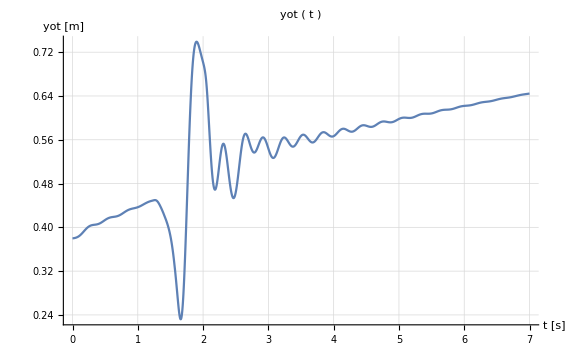
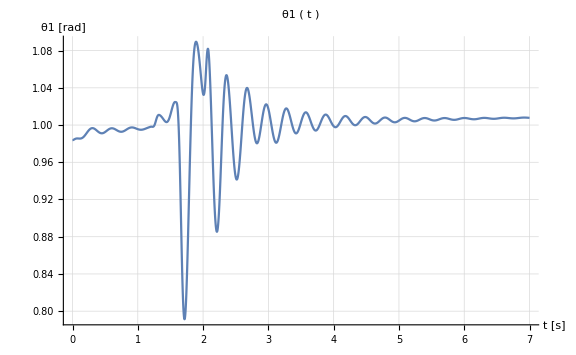
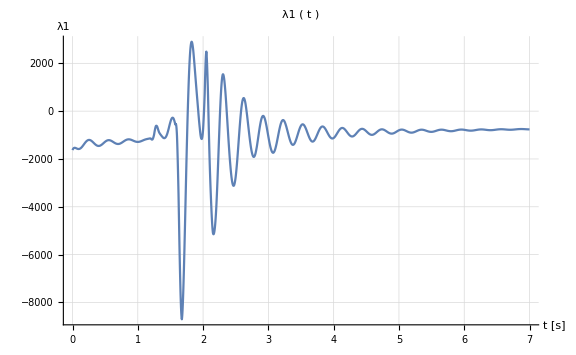
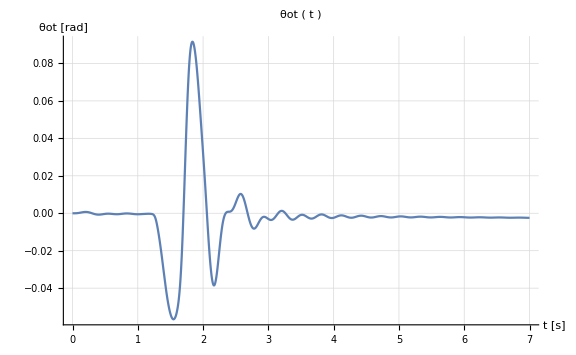
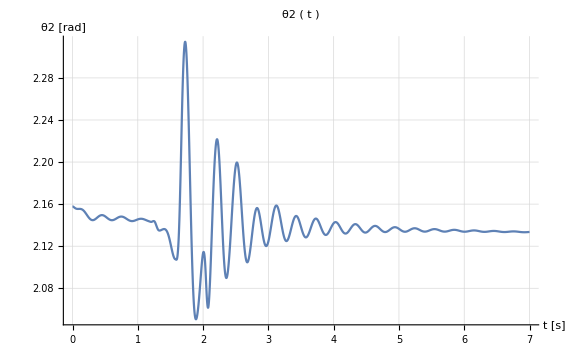
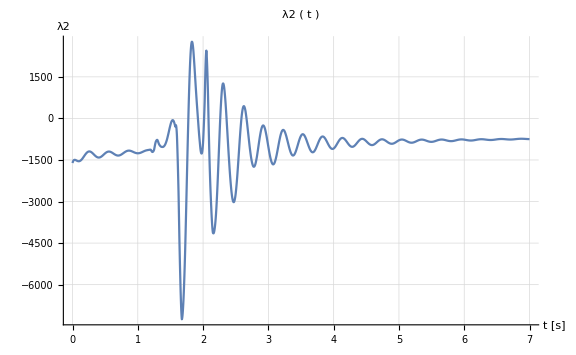
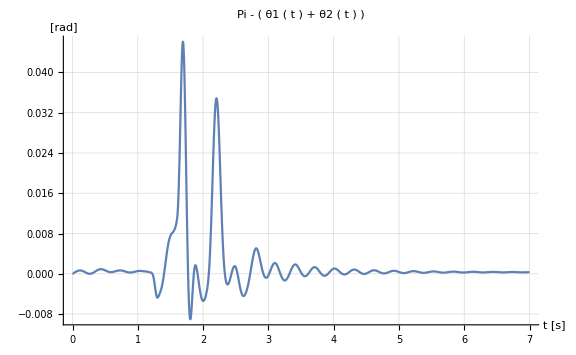
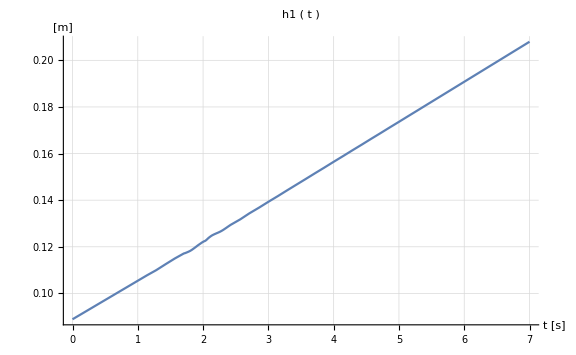

```mathematica
eqs=(𝕖[t]/.{Mot->125,g->9.8,lot->1.8, lb->2, li -> 0.2, ls-> 0.3, k->3000,c->200,zb[t_]->dz[t], zb'[t_]->vz[t], zb''[t_]->D[vz[t],t], θb[t_]->angle[t], θb'[t_]->omega[t], θb''[t_]->D[omega[t],t]})/.Rule->Equal;
Module[{sol, ti=0, ts=7}, sol= NDSolve[Join[eqs, {zot[0]==0.38,θot[0]==0,θ1[0]==0.983783670101104, θ2[0]==2.1578089834886907,zot'[0]==0,θot'[0]==0, θ1'[0]==0, θ2'[0]==0}],{zot,θot,θ1,θ2, λ1,λ2},{t,0,ts}];
{Plot[ Evaluate[(zot[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"yot ( t )", GridLines->Automatic, AxesLabel->{"t [s]","yot [m]"}],
Plot[ Evaluate[(θ1[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"θ1 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","θ1 [rad]"}],
Plot[ Evaluate[(λ1[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"λ1 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","λ1"}],
Plot[ Evaluate[(θot[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"θot ( t )", GridLines->Automatic, AxesLabel->{"t [s]","θot [rad]"}],
Plot[ Evaluate[(θ2[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"θ2 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","θ2 [rad]"}],
Plot[ Evaluate[(λ2[t]/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"λ2 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","λ2"}],
Plot[ Evaluate[(Pi-(θ1[t]+θ2[t])/.sol)],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"Pi - ( θ1 ( t ) + θ2 ( t ) )", GridLines->Automatic, AxesLabel->{"t [s]","[rad]"}],
Plot[ Evaluate[((2/2*Cos[angle[t]] + 0.2*(Cos[angle[t]]*Cos[θ1[t]]-Sin[angle[t]]*Sin[θ1[t]])-1.8/2*Cos[θot[t]])^2 + (dz[t] + 2/2*Sin[angle[t]] + 0.2*(Sin[angle[t]]*Cos[θ1[t]]+Sin[θ1[t]]*Cos[angle[t]]) - (zot[t] + 1.8/2*Sin[θot[t]]))^2)/.sol],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"h1 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","[m]"}],
Plot[ Evaluate[((-1.8/2*Cos[θot[t]]-(-2/2*Cos[angle[t]] + 0.2*(Cos[angle[t]]*Cos[θ2[t]]-Sin[angle[t]]*Sin[θ2[t]])))^2 + (zot[t] - 1.8/2*Sin[θot[t]] - (dz[t] - 2/2*Sin[angle[t]] + 0.2*(Sin[angle[t]]*Cos[θ2[t]]+Cos[angle[t]]*Sin[θ2[t]])))^2)/.sol],{t,ti,ts}, PlotRange->All, ImageSize->Large, LabelStyle->"Subsubsection", PlotLabel->"h2 ( t )", GridLines->Automatic, AxesLabel->{"t [s]","[m]"}]

}
]
```